To ASEN 5007 students: upon downloading this Notebook, check it out by following this procedure.
1.  Compile the initialization cells (1 to 9).  For Mathematica versions <6, use
          Kernel -> Evaluation -> Evaluate Initialization. 
       For  Mathematica versions 6 or higher, use
          Kernel-> Evaluate Initialization Cells
     (To get rid of annoying warning messages, you should initialize twice. )
     Verify that the output  of the initialized cells,  which is  generated by the test statements in blue,
      agrees with Chapter 4 Figures.
2.  Pick Cell 10 by clicking mouse on interior of cell.  Execute by pressing <Shift-Enter> on a
     Windows PC or newer Macs, <Enter> on older Macs.  Check that answers agree with Chapter 4.
     Repeat for Cells 11 and 12.  Note that for these the analysis is symbolic, not numerical, so
     the print utilities of Cell 6 as well as the plot utilities of Cells 7-9 should not be used.
3.  Do HW Exercise 4.1  by writing scripts in Cells 13 & 14. using scripts in Cells 10-11 as "templates"
     Recommendation: go step by step; dont try to write the whole thing and run all at once.

Cell 1: Module to form element stiffness of plane truss element (a 2-node bar) in global coordinates

```mathematica
PlaneBarStiffness[{{x1_,y1_},{x2_,y2_}},Em_,A_]:=Module[
  {c,s,x21=x2-x1,y21=y2-y1,LLe,Le,Ke}, LLe=x21^2+y21^2;
   Le=PowerExpand[Sqrt[LLe]]; c=x21/Le; s=y21/Le;
   Ke=(Em*A/Le)*{{ c^2, c*s,-c^2,-c*s},
                 { c*s, s^2,-s*c,-s^2},
                 {-c^2,-s*c, c^2, s*c},
                 {-s*c,-s^2, s*c, s^2}}; 
   Return[Ke]];
    
Ke= PlaneBarStiffness[{{0,0},{10,10}},100,2*Sqrt[2]];
Print["Numerical Elem Stiff Matrix: ",Ke//MatrixForm];
ClearAll[Em,A,L]; Ke= PlaneBarStiffness[{{0,0},{L,L}},Em,A];
Ke=Simplify[Ke,L>0]; fac=Em*A/(2*Sqrt[2]*L); Kesc=Simplify[Ke/fac];
Print["Symb Elem Stiff Matrix: ",Ke//MatrixForm,
  " = ",fac,"*",Kesc//MatrixForm];
```

Numerical Elem Stiff Matrix: (10 | 10 | -10 | -10
10 | 10 | -10 | -10
-10 | -10 | 10 | 10
-10 | -10 | 10 | 10)

Symb Elem Stiff Matrix: ((A Em)/(2 √2 L) | (A Em)/(2 √2 L) | -(A Em)/(2 √2 L) | -(A Em)/(2 √2 L)
(A Em)/(2 √2 L) | (A Em)/(2 √2 L) | -(A Em)/(2 √2 L) | -(A Em)/(2 √2 L)
-(A Em)/(2 √2 L) | -(A Em)/(2 √2 L) | (A Em)/(2 √2 L) | (A Em)/(2 √2 L)
-(A Em)/(2 √2 L) | -(A Em)/(2 √2 L) | (A Em)/(2 √2 L) | (A Em)/(2 √2 L)) = (A Em)/(2 √2 L)*(1 | 1 | -1 | -1
1 | 1 | -1 | -1
-1 | -1 | 1 | 1
-1 | -1 | 1 | 1)

Cell 2: Module to assemble master stiffness matrix of a plane truss

```mathematica
PlaneTrussMasterStiffness[nodxyz_,elenod_,elemat_,elefab_]:=
  Module[{numele=Length[elenod],numnod=Length[nodxyz],e,eft,
  ni,nj,ncoor,Em,A,Ke,K}, K=Table[0,{2*numnod},{2*numnod}];
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]];
       eft={2*ni-1,2*ni,2*nj-1,2*nj};
       ncoor={nodxyz[[ni]],nodxyz[[nj]]}; 
       Em=elemat[[e]]; A=elefab[[e]];
       Ke=PlaneBarStiffness[ncoor,Em,A]; 
       For [i=1,i<=4,i++, ii=eft[[i]];
            For [j=i,j<=4,j++, jj=eft[[j]];
                 K[[jj,ii]]=K[[ii,jj]]+=Ke[[i,j]]; 
                ];
            ];
      ]; Return[K]];

nodxyz={{0,0},{10,0},{10,10}}; elenod={{1,2},{2,3},{1,3}};
elemat={100,100,100}; elefab={1,1/2,2*Sqrt[2]};  
K=PlaneTrussMasterStiffness[nodxyz,elenod,elemat,elefab];
Print["Master stiffness of example truss: ",K//MatrixForm];
```

Master stiffness of example truss: (20 | 10 | -10 | 0 | -10 | -10
10 | 10 | 0 | 0 | -10 | -10
-10 | 0 | 10 | 0 | 0 | 0
0 | 0 | 0 | 5 | 0 | -5
-10 | -10 | 0 | 0 | 10 | 10
-10 | -10 | 0 | -5 | 10 | 15)

Cell 3:  Modules to apply homogeneous, single-freedom displacement BCs on master stiffness and forces.
Prescribed nonzero displacements are allowed. These modules also work, without any change, for more general FEM models.

```mathematica
AppliedForceVector[nodtag_,nodval_]:= Module[{i,ftag,fval,
 numdof,f}, {ftag,fval}={Flatten[nodtag],Flatten[nodval]};
 numdof=Length[ftag]; f=Table[0,{numdof}]; 
 For [i=1,i<=numdof,i++, If [ftag[[i]]==0, f[[i]]=fval[[i]]]];
 Return[f]]; 

ModifiedMasterStiffness[nodtag_,K_] := Module[
 {i,j,k,n=Length[K],pdof,np,Kmod=K},
  pdof=PrescDispDOFTags[nodtag]; np=Length[pdof]; 
  For [k=1,k<=np,k++, i=pdof[[k]]; 
      For [j=1,j<=n,j++, Kmod[[i,j]]=Kmod[[j,i]]=0];
      Kmod[[i,i]]=1]; 
  Return[Kmod]];  
  
ModifiedNodeForces[nodtag_,nodval_,K_,f_]:= Module[
 {i,j,k,n=Length[K],pdof,pval,np,d,c,fmod=f},
  pdof=PrescDispDOFTags[nodtag]; np=Length[pdof]; 
  pval=PrescDispDOFValues[nodtag,nodval]; c=Table[1,{n}]; 
  For [k=1,k<=np,k++, i=pdof[[k]]; c[[i]]=0];
  For [k=1,k<=np,k++, i=pdof[[k]]; d=pval[[k]]; 
      fmod[[i]]=d; If [d==0, Continue[]];
      For [j=1,j<=n,j++, fmod[[j]]-=K[[i,j]]*c[[j]]*d]; 
      ];  ClearAll[c]; 
  Return[fmod]];
  
PrescDispDOFTags[nodtag_]:= Module[
  {j,n,numnod=Length[nodtag],pdof={},k=0,m},
  For [n=1,n<=numnod,n++, m=Length[nodtag[[n]]];
      For [j=1,j<=m,j++, If [nodtag[[n,j]]>0, 
                AppendTo[pdof,k+j]]]; k+=m;
      ]; Return[pdof]]; 
     
PrescDispDOFValues[nodtag_,nodval_]:= Module[
 {j,n,numnod=Length[nodtag],pval={},k=0,m},
  For [n=1,n<=numnod,n++, m=Length[nodtag[[n]]];
      For [j=1,j<=m,j++, If [nodtag[[n,j]]>0, 
                AppendTo[pval,nodval[[n,j]]]]]; k+=m;
      ]; Return[pval]];
     
nodtag={{1,1},{0,1},{0,0}}; nodval={{-1,2},{0,3},{2,1}};
K={{K11,K12,K13,K14,K15,K16},{K12,K22,K23,K24,K25,K26}, 
   {K13,K23,K33,K34,K35,K36},{K14,K24,K34,K44,K45,K46},
   {K15,K25,K35,K45,K55,K56},{K16,K26,K36,K46,K56,K66}};
Print["K before BC:",K//MatrixForm];
f=AppliedForceVector[nodtag,nodval];
Print["f before BC:",f];    
Kmod=ModifiedMasterStiffness[nodtag,K];
Print["K modified for BC:",Kmod//MatrixForm];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
Print["f modified for BC:",fmod];
```

K before BC:(K11 | K12 | K13 | K14 | K15 | K16
K12 | K22 | K23 | K24 | K25 | K26
K13 | K23 | K33 | K34 | K35 | K36
K14 | K24 | K34 | K44 | K45 | K46
K15 | K25 | K35 | K45 | K55 | K56
K16 | K26 | K36 | K46 | K56 | K66)

f before BC:{0,0,0,0,2,1}

K modified for BC:(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | K33 | 0 | K35 | K36
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | K35 | 0 | K55 | K56
0 | 0 | K36 | 0 | K56 | K66)

f modified for BC:{-1,2,K13-2 K23-3 K34,3,2+K15-2 K25-3 K45,1+K16-2 K26-3 K46}

Cell 4:  Module to compute the internal axial  force in a plane , 2-node bar element

```mathematica
PlaneBarIntForce[{{x1_,y1_},{x2_,y2_}},Em_,A_,ue_]:= Module[
  {x21=x2-x1,y21=y2-y1,dux,duy,LLe,pe}, LLe=x21^2+y21^2;
  dux=ue[[3]]-ue[[1]]; duy=ue[[4]]-ue[[2]];
  pe=(Em*A/LLe)*(x21*dux+y21*duy);
  Return[pe]]; 
  
pe=PlaneBarIntForce[{{0,0},{10,10}},100,2*Sqrt[2],{0,0,0.4,-0.2}];
Print["Bar int force (numerical): ",pe]; 
ClearAll[Em,A,L,ux1,uy1,ux3,uy3];
pe=PlaneBarIntForce[{{0,0},{L,L}},Em,A,{ux1,uy1,ux3,uy3}];
Print["Bar int force (symbolic): ",Simplify[pe]];
```

Bar int force (numerical): 2.82843

Bar int force (symbolic): -(A Em (ux1-ux3+uy1-uy3))/(2 L)

Cell 5:  Modules to get internal forces and stresses in plane truss members

```mathematica
PlaneTrussIntForces[nodxyz_,elenod_,elemat_,elefab_,noddis_]:= 
  Module[{numele=Length[elenod],e,ni,nj,encoor,Em,A,ue,elefor},
  elefor=Table[0,{numele}];
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]];
       encoor={nodxyz[[ni]],nodxyz[[nj]]};  
       Em=elemat[[e]]; A=elefab[[e]];
       ue=Flatten[{noddis[[ni]],noddis[[nj]]}];
       elefor[[e]]=PlaneBarIntForce[encoor,Em,A,ue];
      ]; 
  Return[elefor]];

PlaneTrussStresses[elefab_,elefor_]:= Module[
 {numele=Length[elefab],e,elesig}, elesig=Table[0,{numele}];
  For [e=1,e<=numele,e++, elesig[[e]]=elefor[[e]]/elefab[[e]] ];
  Return[elesig]];

nodxyz={{0,0},{10,0},{10,10}}; elenod={{1,2},{2,3},{1,3}};
elemat={100,100,100}; elefab={1,1/2,2*Sqrt[2]}; 
noddis={{0,0},{0,0},{0.4,-0.2}};
elefor=PlaneTrussIntForces[nodxyz,elenod,elemat,elefab,noddis];
Print["Internal bar forces in example truss:",N[elefor]];
elesig=PlaneTrussStresses[elefab,elefor];
Print["Bar stresses in example truss:",N[elesig]];
```

Internal bar forces in example truss:{0.,-1.,2.82843}

Bar stresses in example truss:{0.,-2.,1.}

Cell 6.  Print utilities and auxiliary modules for array partition

```mathematica
PrintPlaneTrussNodeCoordinates[nodxyz_,title_,digits_]:= Module[
  {numnod=Length[nodxyz],n,x,y,z,d=6,f=6,tab}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++,{x,y}=nodxyz[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[x,{d,f}],PaddedForm[y,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},   
      TableDirections->{Column,Row},TableSpacing->{0,2},
      TableHeadings ->{None,{"node", "x-coor", "y-coor"}}]];
   ClearAll[tab];
   ];
   
PrintPlaneTrussElementData[elenod_,elemat_,elefab_,title_,digits_]:= Module[
  {e,numele=Length[elenod],Em,A,d=6,f=3,tab}, 
  tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, Em=elemat[[e]]; A=elefab[[e]];
        tab[[e]]={ToString[e],ToString[elenod[[e]]],
             PaddedForm[Em,{d,f}],PaddedForm[A,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,2},
         TableHeadings ->{None,{"elem", "nodes", "modulus", "area"}}]];
   ClearAll[tab];
   ];
   
PrintPlaneTrussFreedomActivity[nodtag_,nodval_,title_,digits_]:= Module[
  {numnod=Length[nodtag],n,t,v,tab}, 
   tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, t=nodtag[[n]]; v=nodval[[n]];
        tab[[n]]={ToString[n],
          PaddedForm[t[[1]]],PaddedForm[t[[2]]],
          PaddedForm[v[[1]]],PaddedForm[v[[2]]]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-tag", "y-tag",
                          "x-value", "y-value"}} ]];
   ClearAll[tab];
   ];

PrintPlaneTrussNodeDisplacements[noddis_,title_,digits_]:= Module[
  {numnod=Length[noddis],n,ux,uy,tab,d=6,f=6}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, {ux,uy}=noddis[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[ux,{d,f}],PaddedForm[uy,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-displ", "y-displ"}}]];
   ClearAll[tab];
   ];

PrintPlaneTrussNodeForces[nodfor_,title_,digits_]:= Module[
  {numnod=Length[nodfor],n,fx,fy,tab,d=4,f=4}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, {fx,fy}=nodfor[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[fx,{d,f}],PaddedForm[fy,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-force", "y-force"}}]];
   ClearAll[tab];
   ];
   
PrintPlaneTrussElemForcesAndStresses[elefor_,elesig_,title_,digits_]:= 
  Module[{numele=Length[elefor],e,p,s,d=4,f=4,tab}, 
   tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, p=elefor[[e]]; s=elesig[[e]];
       tab[[e]]={ToString[e],PaddedForm[p,{d,f}],PaddedForm[s,{d,f}]} ]; 
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1}, 
         TableHeadings ->{None,{"elem", "axial force", "axial stress"}}]];
   ClearAll[tab];
   ]; 
 
FlatNodePartVector[nv_]:=Flatten[nv];
           
NodePartFlatVector[nfc_,v_]:= Module[{i,k,m,n,nv={},numnod},
  If [Length[nfc]==0, nv=Partition[v,nfc]];
  If [Length[nfc]>0,  numnod=Length[nfc]; m=0;
      nv=Table[0,{numnod}];   
      For [n=1,n<=numnod,n++, k=nfc[[n]]; 
          nv[[n]]=Table[v[[m+i]],{i,1,k}]; 
          m+=k]];
  Return[nv]];

(*nodxyz={{0,0},{10,0},{10,10}};
PrintPlaneTrussNodeCoordinates[nodxyz,"Test node coord print",{6,4}];
elenod={{1,2},{2,3},{1,3}}; elemat={100,100,100}; elefab=N[{1,1/2,2*Sqrt[2]}];
PrintPlaneTrussElementData[elenod,elemat,elefab,"Test elem data print",{7,3}];
nodtag={{1,1},{0,1},{0,0}}; nodval={{0,0},{0,0},{2,1}};
PrintPlaneTrussFreedomActivity[nodtag,nodval,"Test DOF activity print",{}];
noddis={{0,0},{0,0},{0.4,-0.2}}; 
PrintPlaneTrussNodeDisplacements[noddis,"Test node disp print",{}];
nodfor={{0,0},{0,0},{2,1}}; 
PrintPlaneTrussNodeForces[nodfor,"Test node force print",{8,4}];
elefor={3,4,5}; elesig={3,2,2.5};
PrintPlaneTrussElemForcesAndStresses[elefor,elesig,"Test elem force & stress print",{}];
u={1,2,3,4,5,6}; noddis=NodePartFlatVector[2,u];
Print["u=",u//MatrixForm," noddis=",noddis//MatrixForm];*)
```

Cell 7.  Plot of elements and nodes of plane truss model

```mathematica
PlotPlaneTrussElements[nodxyz_,elenod_,title_,
 {aspect_,imgsiz_,labels_}]:= 
  Module[{numnod=Length[nodxyz],numele=Length[elenod],e,n,ni,nj,
  x,y,xmin,xmax,ymin,ymax,dx,dy,xyc,arat,dfun,pbars={}},
  x=y=Table[0,{numnod}]; 
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=nodxyz[[n]]];
  {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}];
  {dx,dy}={xmax-xmin,ymax-ymin};
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
       xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};      
       AppendTo[pbars,Graphics[Line[xyc]]]];
 arat=AspectRatio->Automatic; If [aspect>0, arat=AspectRatio->aspect];
 dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
 If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
 Show[Graphics[AbsoluteThickness[2]],Graphics[RGBColor[0,0,0]],
      pbars, arat, ImageSize->imgsiz, PlotLabel->title,
      DisplayFunction->dfun ];
 ClearAll[pbars];
 ];

PlotPlaneTrussElementsAndNodes[nodxyz_,elenod_,title_,
 {aspect_,imgsiz_,labels_}]:= Module[{numnod=Length[nodxyz],
  numele=Length[elenod],k=Length[labels],e,n,ni,nj,x,y,xyc,
  xy0,xyn,xmin,xmax,ymin,ymax,elabels,nlabels,fntinfo,
  labnod,frn,fex,fey,labele,fre,fntnam,fntsiz,fntwgt,fntslt,
  black,red,green,blue,yellow,fill,grey,nofill,arat,
  style,dx,dy,dmin,rn,re,ex,ey,elab,nlab,pbars={},
  pecirc={},pelab={},pedisk={},pncirc={},pndisk={},pnlab={} },
  x=y=Table[0,{numnod}];
  {labnod,frn,fex,fey,labele,fre,fntnam,fntsiz,fntwgt,fntslt}=
    {True,0.03,-1.5,0.8,True,0.03,"Times",12,"Plain","Plain"};  
  If [k>=1, nlabels=labels[[1]] ]; 
  If [k>=2, elabels=labels[[2]] ];
  If [k>=3, fntinfo=labels[[3]] ];
  If [Length[nlabels]>=1, labnod=nlabels[[1]] ];
  If [Length[nlabels]>=2, frn=   nlabels[[2]] ];
  If [Length[nlabels]>=3, fex=   nlabels[[3]] ];
  If [Length[nlabels]>=4, fey=   nlabels[[4]] ];
  If [Length[elabels]>=1, labele=elabels[[1]] ];
  If [Length[elabels]>=2, fre=   elabels[[2]] ];
  If [Length[fntinfo]>=1, fntnam=fntinfo[[1]] ];
  If [Length[fntinfo]>=2, fntsiz=fntinfo[[2]] ];
  If [Length[fntinfo]>=3, fntwgt=fntinfo[[3]] ];
  If [Length[fntinfo]>=4, fntslt=fntinfo[[4]] ];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=nodxyz[[n]]];
  {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}];
  {dx,dy}={xmax-xmin,ymax-ymin}; dmin=Min[dx,dy];
  rn=frn*dmin; re=fre*dmin;
  style=TextStyle->{FontFamily->fntnam,FontSize-> fntsiz,
                    FontWeight->fntwgt,FontSlant->fntslt};
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
      xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};
      xy0=(xyc[[1]]+xyc[[2]])/2;
      AppendTo[pbars,Graphics[Line[xyc]]];
      If [labele, elab=ToString[e];
          AppendTo[pedisk, Graphics[Disk[xy0,re]]]; 
          AppendTo[pecirc, Graphics[Circle[xy0,re]]];
          AppendTo[pelab,  Graphics[Text[elab,xy0-{0,0.2*re},style]]]
         ];
      ];
  style=TextStyle->{FontFamily->fntnam,FontSize-> fntsiz,
                    FontWeight->"Bold",FontSlant->"Plain"};
  For [n=1,n<=numnod,n++,  xyn={x[[n]],y[[n]]}; 
      AppendTo[pndisk,  Graphics[Disk[xyn,rn]]];
      AppendTo[pncirc,  Graphics[Circle[xyn,rn]]];
      If [labnod, nlab=ToString[n]; xy0=xyn+{fex,fey}*rn; 
          AppendTo[pnlab, Graphics[Text[nlab,xy0,style]]]];
     ]; 
  {black,red,green,blue,yellow}={RGBColor[0,0,0],RGBColor[1,0,0],
     RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,1,0]};
  {nofill,grey,fill}={GrayLevel[0],GrayLevel[.8],GrayLevel[1]};
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
  Show[Graphics[nofill],Graphics[AbsoluteThickness[3]],
       Graphics[red],pbars, Graphics[AbsoluteThickness[1]],
       Graphics[fill],pndisk, Graphics[nofill],pncirc, 
       Graphics[yellow], pedisk, Graphics[nofill], 
       Graphics[black], pecirc, pelab, pnlab,
       arat, ImageSize->imgsiz, PlotLabel->title,
       DisplayFunction->dfun ];
   ClearAll[pbars,pndisk,pncirc,pedisk,pecirc,pelab];
 ];
 
(*nodxyz={{0,0},{10,5},{10,0},{20,8},{20,0},{30,9},
       {30,0},{40,8},{40,0},{50,5},{50,0},{60,0}};
nodxyz=N[nodxyz];
elenod={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
        {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
        {2,3},{4,5},{6,7},{8,9},{10,11},
        {2,5},{4,7},{7,8},{9,10}};
PlotPlaneTrussElements[nodxyz,elenod,"plain mesh",{0,500,{}}];
labels={{True,0.05,-2.0,2.0},{True,0.15},{"Times",12,"Plain","Italic"}};
PlotPlaneTrussElementsAndNodes[nodxyz,elenod,"mesh with labels",{-1,500,labels}];*)
```

Cell 8.  Plot plane truss deformed shape

```mathematica
PlotPlaneTrussDeformedShape[nodxyz_,elenod_,noddis_,
    amplif_,box_,title_,{aspect_,imgsiz_,colors_}]:= 
  Module[{numnod=Length[nodxyz],numele=Length[elenod],a={},c={},e,k,m,n,
  ni,nj,nf,xbox,ybox,x,y,x0,y0,xmin,xmax,ymin,ymax,dx,dy,xyc,arat,dfun,
  black,red,green,blue,yellow,white,fill,grey,nofill,f,pbars={},p={}},
  x=y=Table[0,{numnod}]; nf=Length[box]; 
  If [nf>0, xbox=ybox=Table[0,{nf}]; 
      For [n=1,n<=nf,n++, {xbox[[n]],ybox[[n]]}=box[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[xbox],Max[xbox],Min[ybox],Max[ybox]}] ];      
  If [nf==0,
      For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=nodxyz[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}] ];
  {dx,dy}={xmax-xmin,ymax-ymin};
  {black,red,green,blue,yellow,white}={RGBColor[0,0,0],RGBColor[1,0,0],
     RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,1,0],RGBColor[1,1,1]};
  {nofill,grey,fill}={GrayLevel[0],GrayLevel[.8],GrayLevel[1]};
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  AppendTo[p,Graphics[AbsoluteThickness[.5]]]; AppendTo[p,Graphics[nofill]];
  enclosingbox={{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}};
  AppendTo[p,Graphics[Line[enclosingbox]]]; 
  AppendTo[p,Graphics[AbsoluteThickness[3]]];
  If [Length[amplif]==0,a={amplif},a=amplif];
  If [Length[colors]==0,c={colors},c=colors]; k=Length[c];
  AppendTo[p,Graphics[black]];
  For [m=1,m<=Length[a],m++, f=a[[m]]; color=c[[Min[m,k]]];
       If [color=="black",  AppendTo[p,Graphics[black]]];
       If [color=="red",    AppendTo[p,Graphics[red]]];
       If [color=="blue",   AppendTo[p,Graphics[blue]]];
       If [color=="green",  AppendTo[p,Graphics[green]]];
       If [color=="yellow", AppendTo[p,Graphics[yellow]]];
       If [color=="white",  AppendTo[p,Graphics[white]]];
       For [n=1,n<=numnod,n++, 
           {x[[n]],y[[n]]}=nodxyz[[n]]+f*noddis[[n]]];
       For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
            xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};      
       AppendTo[p,Graphics[Line[xyc] ]]];
      ];
 dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
 Show[p, arat, ImageSize->imgsiz,PlotLabel->title,DisplayFunction->dfun]; 
 ClearAll[x,y,xbox,ybox,p]; 
 ];
 
(* nodxyz={{0,0},{10,5},{10,0},{20,8},{20,0},{30,9},
       {30,0},{40,8},{40,0},{50,5},{50,0},{60,0}};
noddis={{0,0},{0,-10},{0,-10},{0,-15},{0,-15},{0,-20},
       {0,-20},{0,-15},{0,-15},{0,-10},{0,-10},{0,0}}/20;
nodxyz=N[nodxyz];
elenod={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
        {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
        {2,3},{4,5},{6,7},{8,9},{10,11},
        {2,5},{4,7},{7,8},{9,10}};
box={{0,-8},{60,-8},{60,10},{0,10}};
PlotPlaneTrussDeformedShape[nodxyz,elenod,noddis,{0,1,2},
         box,"original & two deformed shapes",{-1,350,{"red","blue","green"}}]; 
PlotPlaneTrussDeformedShape[nodxyz,elenod,noddis,2.5,box,
         "deformed shape @ mag 2.5",{-1,350,"black"}]; 
PlotPlaneTrussDeformedShape[nodxyz,elenod,noddis,4.0,box,
         "deformed shape @ mag 4",{-1,350,"black"}]; *)
```

Cell 9. Plot plane truss member stresses

```mathematica
PlotPlaneTrussStresses[nodxyz_,elenod_,elesig_,sigfac_,box_,
      title_,{aspect_,imgsiz_,labels_}]:=  Module[
 {numele=Length[elenod],numnod=Length[nodxyz],
  e,n,ni,nj,nc,nf,xyc,x,y,xbox,ybox,xmin,xmax,ymin,ymax,dx,dy,
  smin,smax,fmax,sval,c1,c2,c3,arat,dfun,pbox={},pbars={}},
  x=y=Table[0,{numnod}]; nf=Length[box];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=nodxyz[[n]] ];
  If [nf>0, xbox=ybox=Table[0,{nf}]; 
      For [n=1,n<=nf,n++, {xbox[[n]],ybox[[n]]}=box[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[xbox],Max[xbox],Min[ybox],Max[ybox]}] ];      
  If [nf==0,
      {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}] ];
  {dx,dy}={xmax-xmin,ymax-ymin};
  AppendTo[pbox,Graphics[AbsoluteThickness[.5]]]; 
  AppendTo[pbox,Graphics[GrayLevel[0]]];
  enclosingbox={{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}};
  AppendTo[pbox,Graphics[Line[enclosingbox]]];
  AppendTo[pbox,Graphics[AbsoluteThickness[4]]]; 
  smin=Min[elesig]; smax=Max[elesig]; fmax=Max[Abs[smax],Abs[smin]];
  For [e=1,e<=numele,e++, 
     sval=N[elesig[[e]]*sigfac]; {c1,c2,c3}=LineColor[sval,fmax]; 
     {ni,nj}=elenod[[e]]; xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};    
     AppendTo[pbars,Graphics[RGBColor[c1,c2,c3]]];
     AppendTo[pbars,Graphics[Line[xyc]]]
     ];
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
  Show[pbox,Graphics[RGBColor[0,0,0]],pbars, 
       Background->GrayLevel[0], arat, ImageSize->imgsiz,
       PlotLabel->title, DisplayFunction->dfun];
   ClearAll[pbars,x,y];
 ];

LineColor[f_,fmax_]:= Module[{r,RGBmax={1,0,0},  
   RGBmin={0,0,1}, RGBzero={1,1,1}, RGBout={0,0,0}},
   If [f==0 || fmax==0,   
       Return[RGBzero]];  (* White if f=0 *)
   If [f>fmax || f<-fmax, 
       Return[RGBout ]];  (* Black if outside range *)
   If [f>0, r= N[f/fmax]; 
       Return[r*RGBmax+(1-r)*RGBzero]]; (* positive *)
   If [f<0, r=-N[f/fmax]; 
       Return[r*RGBmin+(1-r)*RGBzero]]; (* negative *)
];

(* nodxyz={{0,0},{10,5},{10,0},{20,8},{20,0},{30,9},
       {30,0},{40,8},{40,0},{50,5},{50,0},{60,0}};
elenod= {{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
         {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
         {2,3},{4,5},{6,7},{8,9},{10,11},
         {2,5},{4,7},{7,8},{9,10}};
elesig={20,20,20,20,20,20,-10,-10,-10,-10,-10,-10,
        15,12,10,12,15,10,18,18,10};
box={{0,-4},{60,-4},{60,10},{0,10}};
PlotPlaneTrussStresses[nodxyz,elenod,elesig,1,box,
   "axial stress in truss members",{0,350,labels}]; *)
```

Cell 10: Driver script to analyze example truss numerically.

Node coords of example truss:

node | x-coor | y-coor
1 |       0 |       0
2 |      10 |       0
3 |      10 |      10

Element data of example truss:

elem | nodes | modulus | area
1 | {1, 2} |      100 |    1.0000
2 | {2, 3} |      100 |    0.5000
3 | {1, 3} |      100 |    2.8284

DOF activity of example truss:

node | x-tag | y-tag | x-value | y-value
1 |  1 |  1 |  0 |  0
2 |  0 |  1 |  0 |  0
3 |  0 |  0 |  2 |  1

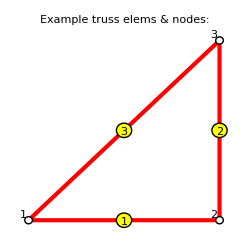

K=(20. | 10. | -10. | 0. | -10. | -10.
10. | 10. | 0. | 0. | -10. | -10.
-10. | 0. | 10. | 0. | 0. | 0.
0. | 0. | 0. | 5. | 0. | -5.
-10. | -10. | 0. | 0. | 10. | 10.
-10. | -10. | 0. | -5. | 10. | 15.) Kmod=(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 10. | 0 | 0. | 0.
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0. | 0 | 10. | 10.
0 | 0 | 0. | 0 | 10. | 15.)

f=(0
0
0
0
2
1) fmod=(0
0
0
0
2
1)

Example truss node displacements:

node | x-displ | y-displ
1 |           0 |           0
2 |           0 |           0
3 |     0.400000 |    -0.200000

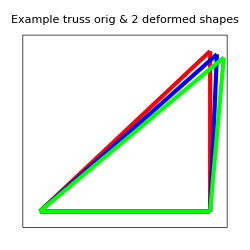

Example truss node forces w/ reactions:

node | x-force | y-force
1 |    -2.000000 |    -2.000000
2 |     0.000000 |     1.000000
3 |     2.000000 |     1.000000

Example truss elem forces & stresses:

elem | axial force | axial stress
1 |        0 |        0
2 |   -1.0000 |   -2.0000
3 |    2.8284 |    1.0000

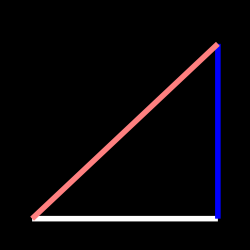

```mathematica
ClearAll[a,Em,A1,A2,A3,fx2,fx3,fy3]; 
a=10; Em=100; A1=1; A2=1/2; A3=2*Sqrt[2]; fx2=0; fx3=2; fy3=1;
nodxyz={{0,0},{a,0},{a,a}}; elenod={{1,2},{2,3},{1,3}};
elemat={Em,Em,Em}; elefab=N[{A1,A2,A3}];
nodtag={{1,1},{0,1},{0,0}}; nodval={{0,0},{fx2,0},{fx3,fy3}};
PrintPlaneTrussNodeCoordinates[nodxyz,"Node coords of example truss:",{6,4}];
PrintPlaneTrussElementData[elenod,elemat,elefab,"Element data of example truss:",{7,4}];
PrintPlaneTrussFreedomActivity[nodtag,nodval,"DOF activity of example truss:",{}];
aspect=1.0; imgsiz=250; box={{0-d,0-d},{10+d,0-d},{10+d,10+d},{0-d,10+d}}/.d->.5; 
labels={{True,0.02,-1.5,1.5},{True,0.04},{"Times",12,"Plain","Italic"}};
PlotPlaneTrussElementsAndNodes[nodxyz,elenod,"Example truss elems & nodes:",
 {aspect,imgsiz,labels}];
K=PlaneTrussMasterStiffness[nodxyz,elenod,elemat,elefab];
f=AppliedForceVector[nodtag,nodval];
Kmod=ModifiedMasterStiffness[nodtag,K];
Print["K=",K//MatrixForm," Kmod=",Kmod//MatrixForm];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
Print["f=",f//MatrixForm," fmod=",fmod//MatrixForm];
u=Simplify[LinearSolve[Kmod,fmod]]; u=Chop[u]; noddis=Partition[u,2];
PrintPlaneTrussNodeDisplacements[noddis,"Example truss node displacements:",{10,6}];
box={{0-d,0-d},{10+d,0-d},{10+d,10+d},{0-d,10+d}}/.d->1; 
PlotPlaneTrussDeformedShape[nodxyz,elenod,noddis,{0,1,2},box,"Example truss"<>
  " orig & 2 deformed shapes",{aspect,imgsiz,{"red","blue","green"}}]; 
f=Simplify[K.u]; nodfor=Partition[f,2];
PrintPlaneTrussNodeForces[nodfor,"Example truss node forces w/ reactions:",{10,6}];
elefor=PlaneTrussIntForces[nodxyz,elenod,elemat,elefab,noddis];
elesig=PlaneTrussStresses[elefab,elefor]; {elefor,elesig}=Chop[{elefor,elesig}];
PrintPlaneTrussElemForcesAndStresses[elefor,elesig,"Example truss elem"<>
       " forces & stresses:",{7,4}];
box={{0-d,0-d},{10+d,0-d},{10+d,10+d},{0-d,10+d}}/.d->.5; 
PlotPlaneTrussStresses[nodxyz,elenod,elesig,1,box,
     "Example truss elem stresses",{aspect,imgsiz,labels}];
```

Cell 11.  Script for analysis of example truss, leaving forces at nodes 2 and  3 symbolic. Do not use print or plot utilities

```mathematica
ClearAll[fx2,fx3,fy3];
nodxyz={{0,0},{10,0},{10,10}}; elenod={{1,2},{2,3},{1,3}};
elemat={100,100,100}; elefab={1,1/2,2*Sqrt[2]}; 
nodtag={{1,1},{0,1},{0,0}}; nodval={{0,0},{fx2,0},{fx3,fy3}};
Print["Node coord of example truss:",nodxyz];
Print["Element data of example truss:",{elenod,elemat,elefab}];
Print["DOF activity of example truss:",{nodtag,nodval}];
K=PlaneTrussMasterStiffness[nodxyz,elenod,elemat,elefab];
f=AppliedForceVector[nodtag,nodval];
Kmod=ModifiedMasterStiffness[nodtag,K];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
u=Simplify[LinearSolve[Kmod,fmod]]; noddis=Partition[u,2]; 
Print["Computed node displacements:",u];
f=Simplify[K.u]; nodfor=Partition[f,2];
Print["Node forces including reactions:",f];
elefor=PlaneTrussIntForces[nodxyz,elenod,elemat,elefab,noddis];
elesig=PlaneTrussStresses[elefab,elefor];
Print["Elem forces: ",elefor]; Print["Elem stresses: ",elesig];
```

Node coord of example truss:{{0,0},{10,0},{10,10}}

Element data of example truss:{{{1,2},{2,3},{1,3}},{100,100,100},{1,1/2,2 √2}}

DOF activity of example truss:{{{1,1},{0,1},{0,0}},{{0,0},{fx2,0},{fx3,fy3}}}

Computed node displacements:{0,0,fx2/10,0,1/10 (3 fx3-2 fy3),1/5 (-fx3+fy3)}

Node forces including reactions:{-fx2-fx3,-fx3,fx2,fx3-fy3,fx3,fy3}

Elem forces: {fx2,-fx3+fy3,√2 (3 fx3-2 fy3+2 (-fx3+fy3))}

Elem stresses: {fx2,2 (-fx3+fy3),1/2 (3 fx3-2 fy3+2 (-fx3+fy3))}

Cell 12.  Example truss with symbolic coordinates, areas and forces. Do not use print or plot utilities

```mathematica
ClearAll[fx2,fx3,fy3,a,b,A1,A2,A3,Em];
nodxyz={{0,0},{a,0},{a,b}}; elenod={{1,2},{2,3},{1,3}};
elemat={Em,Em,Em}; elefab={A1,A2,A3}; 
nodtag={{1,1},{0,1},{0,0}}; nodval={{0,0},{fx2,0},{fx3,fy3}};
Print["Node coord of example truss:",nodxyz];
Print["Element data of example truss:",{elenod,elemat,elefab}];
Print["DOF activity of example truss:",{nodtag,nodval}];
K=PlaneTrussMasterStiffness[nodxyz,elenod,elemat,elefab];
K=Simplify[K,a>0&&b>0];
f=AppliedForceVector[nodtag,nodval];
Kmod=ModifiedMasterStiffness[nodtag,K];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
u=Simplify[LinearSolve[Kmod,fmod],a>0&&b>0]; noddis=Partition[u,2]; 
Print["Computed node displacements:",u];
f=Simplify[K.u,a>0&&b>0]; nodfor=Partition[f,2];
Print["Node forces including reactions:",f];
elefor=PlaneTrussIntForces[nodxyz,elenod,elemat,elefab,noddis];
elefor=Simplify[elefor,a>0&&b>0];
elesig=PlaneTrussStresses[elefab,elefor]; 
elesig=Simplify[elesig,a>0&&b>0];
Print["Elem forces: ",elefor]; Print["Elem stresses: ",elesig];
```

Node coord of example truss:{{0,0},{a,0},{a,b}}

Element data of example truss:{{{1,2},{2,3},{1,3}},{Em,Em,Em},{A1,A2,A3}}

DOF activity of example truss:{{{1,1},{0,1},{0,0}},{{0,0},{fx2,0},{fx3,fy3}}}

Computed node displacements:{0,0,(a fx2)/(A1 Em),0,(A2 (a^2+b^2)^(3/2) fx3+A3 b^2 (b fx3-a fy3))/(a^2 A2 A3 Em),(b (-b fx3+a fy3))/(a A2 Em)}

Node forces including reactions:{-fx2-fx3,-(b fx3)/a,fx2,(b fx3)/a-fy3,fx3,fy3}

Elem forces: {fx2,-(b fx3)/a+fy3,(√(a^2+b^2) fx3)/a}

Elem stresses: {fx2/A1,(-(b fx3)/a+fy3)/A2,(√(a^2+b^2) fx3)/(a A3)}

Cell 13.  Script for Exercise 4.1 - all numerical

Node coords of truss:

node | x-coor | y-coor
1 |     -10 |       0
2 |       0 |       0
3 |      10 |       0
4 |       0 |      10

Element data of truss:

elem | nodes | modulus | area
1 | {1, 2} |      100 |    2.0000
2 | {2, 3} |      100 |    2.0000
3 | {1, 4} |      100 |    4.0000
4 | {3, 4} |      100 |    4.0000
5 | {2, 4} |      100 |    4.0000

DOF activity of truss:

node | x-tag | y-tag | x-value | y-value
1 |  1 |  1 |  0 |  0
2 |  0 |  0 |  0 | -15
3 |  0 |  1 |  0 |  0
4 |  0 |  0 |  0 |  0

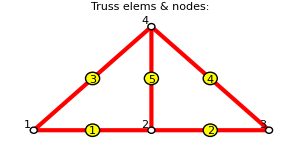

K=(34.1421 | 14.1421 | -20. | 0. | 0 | 0 | -14.1421 | -14.1421
14.1421 | 14.1421 | 0. | 0. | 0 | 0 | -14.1421 | -14.1421
-20. | 0. | 40. | 0. | -20. | 0. | 0. | 0.
0. | 0. | 0. | 40. | 0. | 0. | 0. | -40.
0 | 0 | -20. | 0. | 34.1421 | -14.1421 | -14.1421 | 14.1421
0 | 0 | 0. | 0. | -14.1421 | 14.1421 | 14.1421 | -14.1421
-14.1421 | -14.1421 | 0. | 0. | -14.1421 | 14.1421 | 28.2843 | 0.
-14.1421 | -14.1421 | 0. | -40. | 14.1421 | -14.1421 | 0. | 68.2843) Kmod=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 40. | 0. | -20. | 0 | 0. | 0.
0 | 0 | 0. | 40. | 0. | 0 | 0. | -40.
0 | 0 | -20. | 0. | 34.1421 | 0 | -14.1421 | 14.1421
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0. | 0. | -14.1421 | 0 | 28.2843 | 0.
0 | 0 | 0. | -40. | 14.1421 | 0 | 0. | 68.2843)

f=(0
0
0
-15
0
0
0
0) fmod=(0
0
0
-15
0
0
0
0)

Truss node displacements:

node | x-displ | y-displ
1 |           0 |           0
2 |     0.375000 |    -1.280330
3 |     0.750000 |           0
4 |     0.375000 |    -0.905330

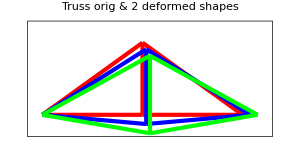

Example truss node forces w/ reactions:

node | x-force | y-force
1 |     1.776357×10^-15 |     7.500000
2 |     0.000000 |   -15.000000
3 |    -1.776357×10^-15 |     7.500000
4 |     0.000000 |     0.000000

Truss elem forces & stresses:

elem | axial force | axial stress
1 |    7.5000 |    3.7500
2 |    7.5000 |    3.7500
3 |  -10.6066 |   -2.6517
4 |  -10.6066 |   -2.6517
5 |   15.0000 |    3.7500

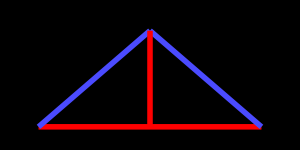

```mathematica
ClearAll[a,Em,A1,A2,A3,fx2,fx3,fy3];
a=10; b=10; Em=100; A1=2; A2=2; A3=4; A4=4; A5=4; fy2=-15; fx3=0; fx2=0; fx4=0; fy4=0;
nodxyz={{-a,0},{0,0},{a,0},{0,b}}; elenod={{1,2},{2,3},{1,4},{3,4},{2,4}};
elemat={Em,Em,Em,Em,Em}; elefab=N[{A1,A2,A3,A4,A5}];
nodtag={{1,1},{0,0},{0,1},{0,0}}; nodval={{0,0},{fx2,fy2},{fx3,0},{fx4,fy4}};
PrintPlaneTrussNodeCoordinates[nodxyz,"Node coords of truss:",{6,4}];
PrintPlaneTrussElementData[elenod,elemat,elefab,"Element data of truss:",{7,4}];
PrintPlaneTrussFreedomActivity[nodtag,nodval,"DOF activity of truss:",{}];
aspect=.5; imgsiz=300; box={{-a-d,0-d},{0+d,0-d},{a+d,0-d},{0-d,b+d}}/.d->.5; 
labels={{True,0.03,-1.8,1.8},{True,0.06},{"Times",12,"Plain","Italic"}};
PlotPlaneTrussElementsAndNodes[nodxyz,elenod,"Truss elems & nodes:",
 {aspect,imgsiz,labels}];
K=PlaneTrussMasterStiffness[nodxyz,elenod,elemat,elefab];
f=AppliedForceVector[nodtag,nodval];
Kmod=ModifiedMasterStiffness[nodtag,K];
Print["K=",K//MatrixForm," Kmod=",Kmod//MatrixForm];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
Print["f=",f//MatrixForm," fmod=",fmod//MatrixForm];
u=Simplify[LinearSolve[Kmod,fmod]]; u=Chop[u]; noddis=Partition[u,2];
PrintPlaneTrussNodeDisplacements[noddis,"Truss node displacements:",{10,6}];
box={{-a-d,0-2*d},{0+d,0-2*d},{a+2*d,0-2*d},{0-d,b+2*d}}/.d->1.5; 
PlotPlaneTrussDeformedShape[nodxyz,elenod,noddis,{0,1,2},box,"Truss"<>
  " orig & 2 deformed shapes",{aspect,imgsiz,{"red","blue","green"}}];
f=Simplify[K.u]; nodfor=Partition[f,2];
PrintPlaneTrussNodeForces[nodfor,"Example truss node forces w/ reactions:",{10,6}];
elefor=PlaneTrussIntForces[nodxyz,elenod,elemat,elefab,noddis];
elesig=PlaneTrussStresses[elefab,elefor]; {elefor,elesig}=Chop[{elefor,elesig}];
PrintPlaneTrussElemForcesAndStresses[elefor,elesig,"Truss elem"<>
       " forces & stresses:",{7,4}];
box={{-a-d,0-d},{0+d,0-d},{a+d,0-d},{0-d,b+d}}/.d->1; 
PlotPlaneTrussStresses[nodxyz,elenod,elesig,1,box,
     "Example truss elem stresses",{aspect,imgsiz,labels}];
```

Cell 14.  Script for Exercise 4.1 w/ symbolic a, b, Em, A and P. Note: Don't forget to 
ClearAll[a,b,Em,A,P] at start! Else it will use numerical  values of previous cell.
Also use Simplify with assumptions a>0&&b>0

```mathematica
ClearAll[a,b,A,A1,A2,A3,A4,A5,fy2,Em];
A1=A; A2=A; A3=2A; A4=2A; A5=2A; fy2=-P;
nodxyz={{-a,0},{0,0},{a,0},{0,b}}; elenod={{1,2},{2,3},{1,4},{3,4},{2,4}};
elemat={Em,Em,Em,Em,Em}; elefab={A1,A2,A3,A4,A5};
nodtag={{1,1},{0,0},{0,1},{0,0}}; nodval={{0,0},{fx2,fy2},{fx3,0},{fx4,fy4}};
Print["Node coord of example truss:",nodxyz];
Print["Element data of example truss:",{elenod,elemat,elefab}];
Print["DOF activity of example truss:",{nodtag,nodval}];
K=PlaneTrussMasterStiffness[nodxyz,elenod,elemat,elefab];
f=AppliedForceVector[nodtag,nodval];
Kmod=ModifiedMasterStiffness[nodtag,K];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
u=Simplify[LinearSolve[Kmod,fmod]]; noddis=Partition[u,2];
u=FullSimplify[u,a>0&&b>0];
Print["Computed node displacements:",u];
f=Simplify[K.u]; nodfor=Partition[f,2];
f=FullSimplify[f,a>0&&b>0];
Print["Node forces including reactions:",f];
elefor=PlaneTrussIntForces[nodxyz,elenod,elemat,elefab,noddis];
elesig=PlaneTrussStresses[elefab,elefor];
elefor=FullSimplify[elefor,a>0&&b>0]; elesig=FullSimplify[elesig,a>0&&b>0];
Print["Elem forces: ",elefor]; Print["Elem stresses: ",elesig];
```

Node coord of example truss:{{-a,0},{0,0},{a,0},{0,b}}

Element data of example truss:{{{1,2},{2,3},{1,4},{3,4},{2,4}},{Em,Em,Em,Em,Em},{A,A,2 A,2 A,2 A}}

DOF activity of example truss:{{{1,1},{0,0},{0,1},{0,0}},{{0,0},{0,-P},{0,0},{0,0}}}

Computed node displacements:{0,0,(a^2 P)/(2 A b Em),-((2 a^3+a^2 √(a^2+b^2)+b^2 (2 b+√(a^2+b^2))) P)/(4 A b^2 Em),(a^2 P)/(A b Em),0,(a^2 P)/(2 A b Em),-((2 a^3+a^2 √(a^2+b^2)+b^2 √(a^2+b^2)) P)/(4 A b^2 Em)}

Node forces including reactions:{0,P/2,0,-P,0,P/2,0,0}

Elem forces: {(a P)/(2 b),(a P)/(2 b),-(√(a^2+b^2) P)/(2 b),-(√(a^2+b^2) P)/(2 b),P}

Elem stresses: {(a P)/(2 A b),(a P)/(2 A b),-(√(a^2+b^2) P)/(4 A b),-(√(a^2+b^2) P)/(4 A b),P/(2 A)}